## New CA Classifiers (random colours)

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs, all 4 classes)

```mathematica
RandomRuleC[n_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
netC[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
dataC[W_Integer,H_Integer,n_Integer]:=Table[RandomRuleC[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

```mathematica
netThreeCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netThreeCC1024[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 1024,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFourCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFiveCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSixCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"drop1"->DropoutLayer[0.2],"conv1"-> ConvolutionLayer[32,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSevenCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netEightCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{8,16}],"flatten"-> FlattenLayer[],"linear"-> 1024,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netNineCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[24,{3,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{12,12}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

### Functions for creating datasets (1D totalistic CAs)

#### k=3, r=1 totalistic (class 4 only)

```mathematica
gen3TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data3T2C[W_Integer,H_Integer,n_Integer]:=Table[gen3TC[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

#### k=4, r=1 totalistic (class 4 only, 1 example)

```mathematica
gen4TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data4TC[W_Integer,H_Integer,n_Integer]:=Table[gen4TC[1004600,W,H]->4,n]
```

#### k=2, r=2 totalistic (all 4 classes)

```mathematica
gen2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data2r2c4C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2C[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4C[W,H,n], data2r2c3C[W,H,n],data2r2c2C[W,H,n],data2r2c1C[W,H,n]]
```

#### k=5, r=1 totalistic (class 4 only)

```mathematica
gen5T4C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T4C[n_Integer,W_Integer,H_Integer]:=Table[gen5T4C[i,W,H]->4,{i,RandomChoice[{781130654,772514435,1151319452,309095787,880862046,973835714,779446817,345466505,535500975,793363571,1052373865,455984785,339227109,1050973846,513368817,91315820,113925357},n]}]
```

### k=5, r=1 totalistic (classes 2/3/4)

```mathematica
gen5TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T4CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->4,{i,RandomChoice[{644218533,491739943,6889640,986144962,1099816682,988971204,300829994,272622024,304100638,626595633},n]}]
data5T3CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->3,{i,RandomChoice[{889082395,541068260,807907479,816180062,650485139,643827745,753940864,871525323,351440311,83501460},n]}]
data5T2CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->2,{i,RandomChoice[{525735659,1022330944,1007796739,495633437,1036827943},n]}]
genData5TCC[W_Integer,H_Integer,n_Integer]:=Join[data5T4CC[W,H,n], data5T3CC[W,H,n],data5T2CC[W,H,n]]
```

### Generate test datasets

#### k=2, r=2 non-totalistic

```mathematica
genk2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak2r2C[W_Integer,H_Integer,n_Integer]:=Table[genk2r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=2, r=3 non-totalistic

```mathematica
genk2r3NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak2r3NT[W_Integer,H_Integer,n_Integer]:=Table[genk2r3NT[i,W,H]->i,{i,RandomInteger[2^2^7-1,n]}]
```

#### k=3, r=1 non-totalistic

```mathematica
genk3r1NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r1NT[W_Integer,H_Integer,n_Integer]:=Table[genk3r1NT[i,W,H]->i,{i,RandomInteger[3^3^3-1,n]}]
```

#### k=3, r=2 totalistic

```mathematica
genk3r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r2C[W_Integer,H_Integer,n_Integer]:=Table[genk3r2C[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

#### k=3, r=3 totalistic

```mathematica
genk3r3C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r3C[W_Integer,H_Integer,n_Integer]:=Table[genk3r3C[i,W,H]->i,{i,RandomChoice[Range[0,14348906],n]}]
```

#### k=4, r=1 non-totalistic

```mathematica
genk4r1NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 4},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r1NT[W_Integer,H_Integer,n_Integer]:=Table[genk4r1NT[i,W,H]->i,{i,RandomInteger[4^4^3-1,n]}]
```

#### k=4, r=1 totalistic

```mathematica
genk4r1C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r1C[W_Integer,H_Integer,n_Integer]:=Table[genk4r1C[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

#### k=4, r=2 totalistic

```mathematica
genk4r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r2C[W_Integer,H_Integer,n_Integer]:=Table[genk4r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=5, r=1 totalistic

```mathematica
gen5T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T2C[n_Integer,W_Integer,H_Integer]:=Table[gen5T2C[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

#### k=6, r=1 totalistic

```mathematica
gen6TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data6TC[n_Integer,W_Integer,H_Integer]:=Table[gen6TC[i,W,H]->i,{i,RandomInteger[2821109907455,n]}]
```

#### k=6, r=2 totalistic

```mathematica
gen6T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data6T2C[n_Integer,W_Integer,H_Integer]:=Table[gen6T2C[i,W,H]->i,{i,RandomInteger[170581728179578208255,n]}]
```

### k=7, r=1 totalistic

```mathematica
gen7TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {7,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data7TC[n_Integer,W_Integer,H_Integer]:=Table[gen7TC[i,W,H]->i,{i,RandomInteger[11398895185373142,n]}]
```

### k=8, r=1 totalistic

```mathematica
gen8TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {8,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data8TC[n_Integer,W_Integer,H_Integer]:=Table[gen8TC[i,W,H]->i,{i,RandomInteger[73786976294838206463,n]}]
```

### Network XIII - Two convolutions, dropout on linear only, BatchNorm

```mathematica
netECA13=netSevenCC512drop[128,128]
```

NetChain[<>]

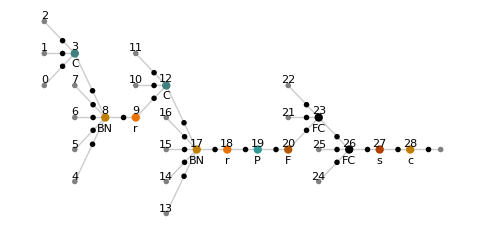

```mathematica
NetInformation[netECA13,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA13,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA13=dataC[128,128,8192];
```

```mathematica
dataTotalistic2BigC13=genData2r2C[128,128,1024];
```

```mathematica
dataTotalistic3BigC13=data3T2C[128,128,1024];
```

```mathematica
dataTotalistic4BigC13=data4TC[128,128,1024];
```

```mathematica
dataTotalistic5BigC13=genData5TCC[128,128,4096];
```

```mathematica
fullTrainingBigC13=Join[dataECA13,dataTotalistic2BigC13,dataTotalistic3BigC13,dataTotalistic4BigC13,dataTotalistic5BigC13];
Length[fullTrainingBigC13]
```

26624

```mathematica
RandomSample[fullTrainingBigC13,20]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4}

```mathematica
RandomSample[fullTrainingBigC13,20]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA12=Import["netECA12-r12.wlnet"]
```

NetChain[<>]

```mathematica
netECA13=NetTrain[netECA13,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA13=Import["netECA13-r20.wlnet"]
```

NetChain[<>]

```mathematica
netECA13=NetTrain[netECA13,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network XIII

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

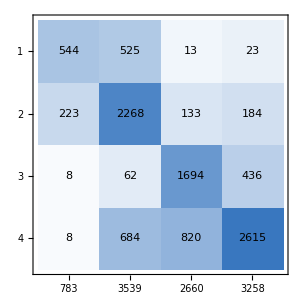
{0.69541,<|1→0.694764,2→0.640859,3→0.636842,4→0.80264|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA13, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA13[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA13[highEntBigC]]
Thread[lowEntBigC->netECA13[lowEntBigC]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Network XIV - BatchNorm, 1024 linear, dropout

```mathematica
netECA14=netEightCC512drop[128,128]
```

NetChain[<>]

```mathematica
netECA14=NetTrain[netECA14,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA14=Import["netECA14-r20.wlnet"]
```

NetChain[<>]

### Generating test data for Network XIV

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4}

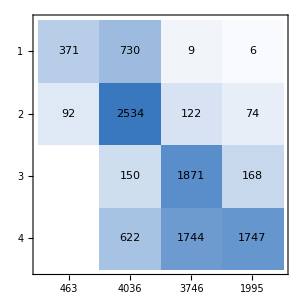
{0.637012,<|1→0.801296,2→0.627849,3→0.499466,4→0.875689|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA14, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA14[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA14[highEntBigC]]
Thread[lowEntBigC->netECA14[lowEntBigC]]
```

{-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Network XV - Transfer learning with pre-trained image recognition net (VGG-16)

```mathematica
netECA15=NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
subNet=NetTake[netECA15,{"conv1_1","flatten_0"}]
```

NetChain[<>]

```mathematica
joinedNet=NetJoin[subNet,NetChain@<|"linear_new"->LinearLayer[1024],"linear_out"->LinearLayer[4],"prob"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

NetChain[<>]

```mathematica
netECA15final=NetPrepend[joinedNet,{"augment"->ImageAugmentationLayer[{224,224}]},"Input"->NetExtract[joinedNet,"Input"]]
```

NetChain[<>]

```mathematica
dataECA15=dataC[224,224,8192];
```

```mathematica
dataTotalistic2BigC15=genData2r2C[224,224,1024];
```

```mathematica
dataTotalistic3BigC15=data3T2C[224,224,512];
```

```mathematica
dataTotalistic4BigC15=data4TC[224,224,512];
```

```mathematica
dataTotalistic5BigC15=genData5TCC[224,224,1024];
```

```mathematica
fullTrainingBigC15=Join[dataECA15,dataTotalistic2BigC15,dataTotalistic3BigC15,dataTotalistic4BigC15,dataTotalistic5BigC15];
Length[fullTrainingBigC15]
```

16384

```mathematica
RandomSample[fullTrainingBigC15,20]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→2}

```mathematica
netECA15final=NetTrain[netECA15final,fullTrainingBigC15,MaxTrainingRounds->5,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir},LearningRateMultipliers->{"linear_new"->1,"linear_out"->1,_->0}]
```

### Network XVI - Three convolutions, dropout on linear only, BatchNorm

```mathematica
netECA16=netNineCC512drop[128,128]
```

NetChain[<>]

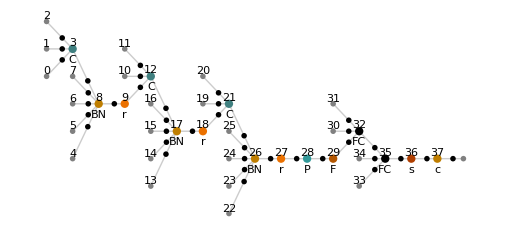

```mathematica
NetInformation[netECA16,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA16,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA16=dataC[128,128,8192];
```

```mathematica
dataTotalistic2BigC16=genData2r2C[128,128,1024];
```

```mathematica
dataTotalistic3BigC16=data3T2C[128,128,1024];
```

```mathematica
dataTotalistic4BigC16=data4TC[128,128,1024];
```

```mathematica
dataTotalistic5BigC16=genData5TCC[128,128,4096];
```

```mathematica
fullTrainingBigC16=Join[dataECA16,dataTotalistic2BigC16,dataTotalistic3BigC16,dataTotalistic4BigC16,dataTotalistic5BigC16];
Length[fullTrainingBigC16]
```

26624

```mathematica
RandomSample[fullTrainingBigC16,20]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→1,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→2}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA16=NetTrain[netECA16,fullTrainingBigC16,MaxTrainingRounds->20,BatchSize->256,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA16=Import["netECA16-r20.wlnet"]
```

```mathematica
netECA16=NetTrain[netECA16,fullTrainingBigC16,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

### Generate test data for Network XVI

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA16=Import["netECA16-r20.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→4}

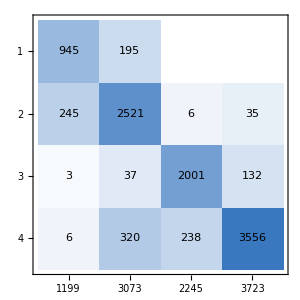
{0.881152,<|1→0.788157,2→0.820371,3→0.891314,4→0.955144|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA16, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA16[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA16[highEntBigC]]
Thread[lowEntBigC->netECA16[lowEntBigC]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4}

### Testing Network XVI on unseen CA rule spaces

#### 2-colour non-totalistic, range 2

```mathematica
test4Data2kr2C16 = datak2r2C[128,128,8];
Thread[test4Data2kr2C16->netECA16[Keys@test4Data2kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→2190952680)→{4→0.00828426,3→0.991715},(-Graphics-→452760995)→{4→0.0697559,3→0.930224},(-Graphics-→1629569269)→{1→0.0640571,2→0.933385},(-Graphics-→2240312508)→{3→0.118588,2→0.799924},(-Graphics-→482556537)→{4→0.0846837,3→0.914806},(-Graphics-→1597446147)→{4→0.248082,2→0.566962},(-Graphics-→2592600046)→{3→0.111319,2→0.801882},(-Graphics-→2548551192)→{4→0.0691249,3→0.930844}}

#### 2-colour non-totalistic, range 3

```mathematica
test4Data2kr3C16 = datak2r3NT[128,128,8];
Thread[test4Data2kr3C16->netECA16[Keys@test4Data2kr3C16,{"TopProbabilities",2}]]
```

{(-Graphics-→192512040898603851305563821357837920322)→{3→0.277165,4→0.649887},(-Graphics-→268814102680703659513703900569271732433)→{4→0.410444,3→0.585722},(-Graphics-→234179531560333249757404371202280747219)→{4→0.223487,3→0.776512},(-Graphics-→25383678045436598053387497115518594687)→{3→0.0605962,4→0.938855},(-Graphics-→198476619696798272452027738615092731693)→{4→0.0598654,3→0.940094},(-Graphics-→338073225958790856870507077934439630490)→{4→0.354784,2→0.643357},(-Graphics-→327367588377016075437244034595798938936)→{3→0.0133918,4→0.986511},(-Graphics-→64210583158946454226752791209536621761)→{3→0.327669,4→0.672036}}

#### 3-colour non-totalistic, range 1

```mathematica
test4Data3kr1C16 = datak3r1NT[128,128,8];
Thread[test4Data3kr1C16->netECA16[Keys@test4Data3kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→2473850236436)→{4→0.00291686,2→0.996637},(-Graphics-→2347219495748)→{4→0.158002,3→0.841998},(-Graphics-→851165089277)→{4→0.423993,2→0.575989},(-Graphics-→6208032017586)→{3→0.291377,2→0.418742},(-Graphics-→7322710481736)→{3→0.0417726,4→0.95685},(-Graphics-→4864402493091)→{4→0.075809,3→0.924191},(-Graphics-→4457586281952)→{1→0.000285388,2→0.999711},(-Graphics-→7458524800199)→{1→0.00964059,2→0.990356}}

#### 3-colour totalistic, range 2

```mathematica
test4Data3kr2C16 = datak3r2C[128,128,8];
Thread[test4Data3kr2C16->netECA16[Keys@test4Data3kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→22138)→{3→0.432672,4→0.567328},(-Graphics-→15962)→{4→0.0786194,3→0.921381},(-Graphics-→14359)→{3→0.285852,4→0.713315},(-Graphics-→84285)→{3→0.0456504,4→0.953803},(-Graphics-→88604)→{2→0.0365346,1→0.963464},(-Graphics-→105626)→{1→0.00134017,2→0.998622},(-Graphics-→131100)→{4→0.126999,3→0.873001},(-Graphics-→74382)→{4→0.00764391,3→0.992356}}

#### 3-colour totalistic, range 3

```mathematica
test4Data3kr3C16 = datak3r3C[128,128,8];
Thread[test4Data3kr3C16->netECA16[Keys@test4Data3kr3C16,{"TopProbabilities",2}]]
```

{(-Graphics-→13965620)→{4→0.129201,2→0.823269},(-Graphics-→2834469)→{4→0.00281357,3→0.997186},(-Graphics-→4592009)→{3→0.13601,4→0.86399},(-Graphics-→5085210)→{3→0.0479753,4→0.952025},(-Graphics-→5151167)→{3→0.491086,4→0.508913},(-Graphics-→12114410)→{4→0.230657,3→0.769343},(-Graphics-→2816030)→{3→0.0175618,4→0.982438},(-Graphics-→5685248)→{4→0.169957,3→0.830043}}

#### 4-colour non-totalistic, range 1

```mathematica
test4Data4kr1C16 = datak4r1NT[128,128,8];
Thread[test4Data4kr1C16->netECA16[Keys@test4Data4kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→24580558256129418488831337020120596557)→{4→0.0591881,3→0.940812},(-Graphics-→320024124365477690559134299487833253915)→{4→0.0960659,3→0.903922},(-Graphics-→106948342425382488412301983608519263756)→{4→0.112148,3→0.887845},(-Graphics-→86351110305322460128720263758500775714)→{4→0.210001,2→0.788983},(-Graphics-→77433156501235157602475680472280279759)→{2→0.474925,4→0.524655},(-Graphics-→596023145536016638713432023142370353)→{4→0.0241829,3→0.975817},(-Graphics-→185023579802380747817653061728311135906)→{4→0.0751294,3→0.924824},(-Graphics-→273295602940247217835514841293393314396)→{4→0.201624,3→0.797811}}

#### 4-colour totalistic, range 2

```mathematica
test4Data4kr2C16 = datak4r2C[128,128,8];
Thread[test4Data4kr2C16->netECA16[Keys@test4Data4kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→1806102772)→{4→0.0919674,3→0.908033},(-Graphics-→1872979601)→{4→0.349808,3→0.650192},(-Graphics-→3186088319)→{4→0.0374994,3→0.962501},(-Graphics-→271280936)→{4→0.000901956,3→0.999098},(-Graphics-→1898315512)→{4→0.00981637,3→0.990184},(-Graphics-→3684955635)→{3→0.190496,4→0.809504},(-Graphics-→3752298976)→{4→0.0541872,3→0.945813},(-Graphics-→2566352175)→{3→0.0379958,4→0.962004}}

#### 5-colour totalistic, range 1

```mathematica
test4Data5kr1C16 = data5T2C[8,128,128];
Thread[test4Data5kr1C16->netECA16[Keys@test4Data5kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→407892722)→{4→0.445788,3→0.554177},(-Graphics-→638248908)→{4→0.0228094,3→0.97719},(-Graphics-→710896859)→{1→0.00682515,2→0.987484},(-Graphics-→966655073)→{3→0.161564,4→0.837494},(-Graphics-→411613899)→{4→0.0818569,3→0.918143},(-Graphics-→554163154)→{1→0.00503217,2→0.99461},(-Graphics-→676388552)→{4→0.300972,3→0.698657},(-Graphics-→134083721)→{4→0.129426,3→0.870558}}

#### 6-colour totalistic, range 1

```mathematica
test4Data6kr1C16 = data6TC[8,128,128];
Thread[test4Data6kr1C16->netECA16[Keys@test4Data6kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→930044739883)→{4→0.0671154,3→0.932882},(-Graphics-→1609022451969)→{3→0.328033,4→0.671644},(-Graphics-→2498882479071)→{3→0.00867874,4→0.991315},(-Graphics-→250248309401)→{4→0.0365648,3→0.963435},(-Graphics-→2382182512148)→{1→0.0000910832,2→0.999907},(-Graphics-→1552150347166)→{3→0.119638,4→0.880047},(-Graphics-→72403648176)→{4→0.0055479,3→0.994452},(-Graphics-→621012387361)→{2→0.284038,4→0.713633}}

#### 6-colour totalistic, range 2

```mathematica
test4Data6kr2C16 = data6T2C[8,128,128];
Thread[test4Data6kr2C16->netECA16[Keys@test4Data6kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→68918261516486585431)→{3→0.389806,4→0.607333},(-Graphics-→81547637786331552954)→{3→0.380046,4→0.619953},(-Graphics-→27230916895777366626)→{4→0.111816,3→0.888135},(-Graphics-→88349935939278240116)→{3→0.0195468,4→0.980452},(-Graphics-→106204901720869169245)→{4→0.0393044,3→0.960696},(-Graphics-→12255387586435585434)→{4→0.0196859,3→0.980314},(-Graphics-→52226526820494761535)→{4→0.106148,3→0.893852},(-Graphics-→62760542193998695205)→{4→0.333915,3→0.666084}}

#### 7-colour totalistic, range 1

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→4083567256423497)→{3→0.393178,4→0.491438},(-Graphics-→10897379800108189)→{3→0.145139,4→0.851377},(-Graphics-→9696870909078497)→{3→0.0940102,4→0.905966},(-Graphics-→6997538642841063)→{4→0.105674,3→0.894326},(-Graphics-→6333682656512326)→{4→0.295264,3→0.704461},(-Graphics-→4047667631402393)→{3→0.292137,4→0.707841},(-Graphics-→10474570668116194)→{4→0.291514,3→0.708433},(-Graphics-→8413297417285155)→{4→0.269519,3→0.730477}}

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→11101279181647317)→{4→0.250155,3→0.749527},(-Graphics-→11021473369162315)→{4→0.0524406,3→0.947559},(-Graphics-→4867969352368900)→{3→0.253496,4→0.746471},(-Graphics-→1278729909433340)→{3→0.12299,4→0.876993},(-Graphics-→3704845844743256)→{4→0.466395,3→0.533503},(-Graphics-→4223308668057052)→{4→0.488556,3→0.511443},(-Graphics-→6902850650536429)→{3→0.215413,4→0.784586},(-Graphics-→1926864005427175)→{3→0.0946958,4→0.904136}}

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→203595605949565)→{4→0.190292,3→0.809707},(-Graphics-→10033010686584540)→{4→0.156969,3→0.843031},(-Graphics-→7330900949575011)→{4→0.132693,3→0.866858},(-Graphics-→2943550672701792)→{3→0.116083,4→0.883885},(-Graphics-→3468324643172098)→{4→0.0991377,3→0.900457},(-Graphics-→6736336766801222)→{3→0.498866,4→0.501134},(-Graphics-→1466636402463332)→{3→0.218265,4→0.781734},(-Graphics-→1428111228778929)→{3→0.0577248,4→0.925458}}

#### 8-colour totalistic, range 1

```mathematica
test4Data8kr1C16 = data8TC[8,128,128];
Thread[test4Data8kr1C16->netECA16[Keys@test4Data8kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→42020590261131320575)→{4→0.0117574,3→0.988243},(-Graphics-→12610707415579864791)→{4→0.0178909,3→0.982109},(-Graphics-→15365143935027257744)→{1→0.0201417,2→0.960127},(-Graphics-→20096665423769445584)→{4→0.0368129,3→0.963187},(-Graphics-→15686501956369591456)→{3→0.111799,4→0.88817},(-Graphics-→46724218297933137114)→{4→0.123036,3→0.876962},(-Graphics-→44175329969224582408)→{4→0.0345722,2→0.961729},(-Graphics-→65643433669628134604)→{4→0.355071,3→0.643197}}

```mathematica
test4Data8kr1C16 = data8TC[8,128,128];
Thread[test4Data8kr1C16->netECA16[Keys@test4Data8kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→36507401174866450102)→{3→0.244239,4→0.75576},(-Graphics-→36629210896102279370)→{4→0.2431,3→0.753856},(-Graphics-→50599399972817837073)→{4→0.24465,3→0.75535},(-Graphics-→62920725793807162408)→{4→0.240564,3→0.759435},(-Graphics-→37059387199693125873)→{4→0.0784766,3→0.921523},(-Graphics-→16229780842690144670)→{4→0.0229385,3→0.977062},(-Graphics-→41966635277478833399)→{4→0.243929,3→0.755756},(-Graphics-→72502378842348778161)→{4→0.376498,2→0.619948}}